```mathematica
Subsets[Range[5],{2}]
```

{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}

```mathematica
Table[ChromaticPolynomial[EdgeContract[plantri8,s],4],{s,Subsets[Range[5],{2}]}]
```

{528,528,528,528,528,528,528,528,528,528}

```mathematica
Table[ChromaticPolynomial[EdgeContract[plantri8,{s[[1]]<->s[[2]],s[[3]]<->s[[4]]}],4],{s,Subsets[Range[5],{4}]}]
```

{768,744,864,624,528}

```mathematica
EmbedGraph5
```

```mathematica
EmbedGraphInPlantri8[k_]:=EmbedGraphInPlantri8[allGraphs5,k]
```

```mathematica
Table[ChromaticPolynomial[EmbedGraphInPlantri8[k],4],{k,alfa1s}]
```

{72,192,0,192,72}

```mathematica
Table[ShowGraph5Least[k]->ChromaticPolynomial[EmbedGraphInPlantri8[k],4],{k,quads}]
```

{-Graphics-360850→216,-Graphics-296050→144,-Graphics-295270→144,-Graphics-317110→216,-Graphics-295510→264}

```mathematica
Table[ShowGraph5Least[k]->ChromaticPolynomial[EmbedGraphInPlantri8[k],4],{k,alfa1s}]
```

{-Graphics-361660→72,-Graphics-317380→192,-Graphics-296080→0,-Graphics-361120→192,-Graphics-317140→72}

```mathematica
allGraphs5[36166,"parents"]
```

{36138,36138,36003,36004,35977,35434,35434,33807,33808,33781,23041,23044,22789,22792,22315,22063,16077,16078,16051,14044,14044,14044,14044,1171,1174,445}

```mathematica
alfa1Key
```

36166

```mathematica
alfa1s
```

{36166,31738,29608,36112,31714}

```mathematica
29608
```

```mathematica
ShowGraph5Least[7738]->Table[Map[ShowGraph5Least[#]->ChromaticPolynomial[EmbedGraphInPlantri8[#],4]&,child],{child,DeleteDuplicates[allGraphs5[7738,"children"]]}]
```

-Graphics-77380→{{-Graphics-296080→0,-Graphics-514780→120}}

```mathematica
ShowGraph5Least[29446]->allGraphs5[29446,"colofour"]/.RepGraph["C"]
```

-Graphics-294460→-Graphics-296080+-Graphics-295270

```mathematica
Sqrt[144]
```

12

```mathematica
Monitor[TableForm
[
Sort[
Table[
Labeled[ShowGraph5Least[parent],Style[ChromaticPolynomial[EmbedGraphInPlantri8[parent],4],Underlined]]->Table[Map[ShowGraph5Least[#]->ChromaticPolynomial[EmbedGraphInPlantri8[#],4]&,child],{child,DeleteDuplicates[allGraphs5[parent,"children"]]}],
{parent,Sort[DeleteDuplicates[allGraphs5[36166,"parents"]]]}],
Length[#1[[2]]]<Length[#2[[2]]]&]
],
{child,parent}
]
```

-Graphics-361380168→{{-Graphics-361660→72,-Graphics-361940→96}}
-Graphics-360040288→{{-Graphics-360850→216,-Graphics-361660→72}}
-Graphics-354340192→{{-Graphics-361660→72,-Graphics-368980→120}}
-Graphics-230440216→{{-Graphics-296050→144,-Graphics-361660→72}}
-Graphics-140441456→{{-Graphics-361660→72,-Graphics-582881→384}}
-Graphics-360030480→{{-Graphics-360840→408,-Graphics-361660→72},{-Graphics-360040→288,-Graphics-360860→192}}
-Graphics-359771480→{{-Graphics-360580→408,-Graphics-361660→72},{-Graphics-360040→288,-Graphics-361120→192}}
-Graphics-338080456→{{-Graphics-360040→288,-Graphics-382810→168},{-Graphics-338890→384,-Graphics-361660→72}}
-Graphics-230411216→{{-Graphics-296020→144,-Graphics-361660→72},{-Graphics-230440→216,-Graphics-296080→0}}
-Graphics-227921552→{{-Graphics-293531→480,-Graphics-361660→72},{-Graphics-230440→216,-Graphics-298571→336}}
-Graphics-223150408→{{-Graphics-288760→336,-Graphics-361660→72},{-Graphics-230440→216,-Graphics-303340→192}}
-Graphics-160781768→{{-Graphics-360040→288,-Graphics-560111→480},{-Graphics-161591→696,-Graphics-361660→72}}
-Graphics-11740528→{{-Graphics-230440→216,-Graphics-514750→312},{-Graphics-77350→456,-Graphics-361660→72}}
-Graphics-338070648→{{-Graphics-360030→480,-Graphics-382810→168},{-Graphics-338880→576,-Graphics-361660→72},{-Graphics-338080→456,-Graphics-360860→192}}
-Graphics-337812864→{{-Graphics-359771→480,-Graphics-382541→384},{-Graphics-338621→792,-Graphics-361660→72},{-Graphics-338080→456,-Graphics-339160→408}}
-Graphics-227892552→{{-Graphics-293501→480,-Graphics-361660→72},{-Graphics-230411→216,-Graphics-298571→336},{-Graphics-227921→552,-Graphics-296080→0}}
-Graphics-2206321008→{{-Graphics-286242→936,-Graphics-361660→72},{-Graphics-227921→552,-Graphics-300821→456},{-Graphics-223150→408,-Graphics-291282→600}}
-Graphics-1607721248→{{-Graphics-360030→480,-Graphics-560102→768},{-Graphics-161582→1176,-Graphics-361660→72},{-Graphics-160781→768,-Graphics-161601→480}}
-Graphics-160512960→{{-Graphics-359771→480,-Graphics-560111→480},{-Graphics-161321→888,-Graphics-361660→72},{-Graphics-160781→768,-Graphics-361120→192}}
-Graphics-11712648→{{-Graphics-230411→216,-Graphics-514721→432},{-Graphics-77321→576,-Graphics-361660→72},{-Graphics-11740→528,-Graphics-77380→120}}
-Graphics-4450720→{{-Graphics-223150→408,-Graphics-514750→312},{-Graphics-70060→648,-Graphics-361660→72},{-Graphics-11740→528,-Graphics-303340→192}}

```mathematica
Monitor[TableForm
[
Sort[
Table[
Labeled[ShowGraph5Least[parent],Style[ChromaticPolynomial[EmbedGraphInPlantri8[parent],4],Underlined]]->Table[Map[ShowGraph5Least[#]->ChromaticPolynomial[EmbedGraphInPlantri8[#],4]&,child],{child,DeleteDuplicates[allGraphs5[parent,"children"]]}],
{parent,Sort[DeleteDuplicates[allGraphs5[29608,"parents"]]]}],
Length[#1[[2]]]<Length[#2[[2]]]&]
],
{child,parent}
]
```

-Graphics-296020144→{{-Graphics-296050→144,-Graphics-296080→0}}
-Graphics-294460144→{{-Graphics-295270→144,-Graphics-296080→0}}
-Graphics-293281264→{{-Graphics-296080→0,-Graphics-298881→264}}
-Graphics-223180120→{{-Graphics-296080→0,-Graphics-368980→120}}
-Graphics-77380120→{{-Graphics-296080→0,-Graphics-514780→120}}
-Graphics-295740384→{{-Graphics-296020→144,-Graphics-296330→240},{-Graphics-295770→384,-Graphics-296080→0}}
-Graphics-294361480→{{-Graphics-295171→480,-Graphics-296080→0},{-Graphics-294460→144,-Graphics-295371→336}}
-Graphics-293501480→{{-Graphics-296020→144,-Graphics-298571→336},{-Graphics-293531→480,-Graphics-296080→0}}
-Graphics-291760384→{{-Graphics-294460→144,-Graphics-297970→240},{-Graphics-292570→384,-Graphics-296080→0}}
-Graphics-288730336→{{-Graphics-296020→144,-Graphics-303340→192},{-Graphics-288760→336,-Graphics-296080→0}}
-Graphics-272591216→{{-Graphics-294460→144,-Graphics-317140→72},{-Graphics-273400→216,-Graphics-296080→0}}
-Graphics-230411216→{{-Graphics-296020→144,-Graphics-361660→72},{-Graphics-230440→216,-Graphics-296080→0}}
-Graphics-97630336→{{-Graphics-294460→144,-Graphics-492100→192},{-Graphics-98440→336,-Graphics-296080→0}}
-Graphics-288450576→{{-Graphics-295740→384,-Graphics-303340→192},{-Graphics-288730→336,-Graphics-296330→240},{-Graphics-288480→576,-Graphics-296080→0}}
-Graphics-286212936→{{-Graphics-293501→480,-Graphics-300821→456},{-Graphics-288730→336,-Graphics-291282→600},{-Graphics-286242→936,-Graphics-296080→0}}
-Graphics-272492552→{{-Graphics-294361→480,-Graphics-317140→72},{-Graphics-273301→552,-Graphics-296080→0},{-Graphics-272591→216,-Graphics-295371→336}}
-Graphics-269892552→{{-Graphics-291760→384,-Graphics-314440→168},{-Graphics-272591→216,-Graphics-276101→336},{-Graphics-270701→552,-Graphics-296080→0}}
-Graphics-230132552→{{-Graphics-295740→384,-Graphics-361380→168},{-Graphics-230411→216,-Graphics-230721→336},{-Graphics-230161→552,-Graphics-296080→0}}
-Graphics-227892552→{{-Graphics-293501→480,-Graphics-361660→72},{-Graphics-230411→216,-Graphics-298571→336},{-Graphics-227921→552,-Graphics-296080→0}}
-Graphics-97532936→{{-Graphics-294361→480,-Graphics-492001→456},{-Graphics-98342→936,-Graphics-296080→0},{-Graphics-97630→336,-Graphics-98542→600}}
-Graphics-94930576→{{-Graphics-291760→384,-Graphics-492100→192},{-Graphics-97630→336,-Graphics-297970→240},{-Graphics-95740→576,-Graphics-296080→0}}

```mathematica
Table[ShowGraph5Least[k]->ChromaticPolynomial[EmbedGraphInPlantri8[k],4],{k,Sort[DeleteDuplicates[allGraphs5[29608,"parents"]]]}]
```

{-Graphics-77380→120,-Graphics-94930→576,-Graphics-97532→936,-Graphics-97630→336,-Graphics-223180→120,-Graphics-227892→552,-Graphics-230132→552,-Graphics-230411→216,-Graphics-269892→552,-Graphics-272492→552,-Graphics-272591→216,-Graphics-286212→936,-Graphics-288450→576,-Graphics-288730→336,-Graphics-291760→384,-Graphics-293281→264,-Graphics-293501→480,-Graphics-294361→480,-Graphics-294460→144,-Graphics-295740→384,-Graphics-296020→144}

```mathematica
allGraphs5[alfa1Key,"parents"]
```

{36138,36138,36003,36004,35977,35434,35434,33807,33808,33781,23041,23044,22789,22792,22315,22063,16077,16078,16051,14044,14044,14044,14044,1171,1174,445}

```mathematica
Table[ShowGraph5Least[k]->ChromaticPolynomial[EmbedGraphInPlantri8[k],4],{k,alfas}]
```

{-Graphics-359771→480,-Graphics-316811→480,-Graphics-230411→216,-Graphics-208031→648,-Graphics-272591→216}

```mathematica
halfgods={29446,29469,31684,36058,33889,22990,23044,22237,25141}
```

{29446,29469,31684,36058,33889,22990,23044,22237,25141}

```mathematica
Table[ShowGraph5Least[k]->ChromaticPolynomial[EmbedGraphInPlantri8[k],4],{k,{29577,29257}}]
```

{-Graphics-295770→384,-Graphics-292570→384}

```mathematica
Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==4&&EdgeCount[g]==5]&]
```

{29529,29517,29513,29542,29506,29602,29577,29446,29469,29417,29766,29737,29677,29282,29305,29257,29353,29209,30244,30172,30010,28804,28876,29038,31708,31684,31468,30981,27340,27364,27580,28065,26609,36084,36058,36004,35353,33889,22964,22990,23044,23689,22237,25141,20785,49206,49204,49198,48451,46939,42403,9842,9844,9850,10543,9139,11947,7735,16159,3523}

```mathematica
Table[ShowGraph5Least[k]->ChromaticPolynomial[EmbedGraphInPlantri8[k],4],{k,Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==4&&EdgeCount[g]==5&&!MemberQ[allGraphs5[#,"vertexsets"],{1,2}]]&&!MemberQ[allGraphs5[#,"vertexsets"],{2,3}]&&!MemberQ[allGraphs5[#,"vertexsets"],{3,4}]&&!MemberQ[allGraphs5[#,"vertexsets"],{4,5}]&&!MemberQ[allGraphs5[#,"vertexsets"],{1,5}]&]}]
```

{-Graphics-295171→480,-Graphics-295420→1008,-Graphics-296020→144,-Graphics-295770→384,-Graphics-294460→144,-Graphics-294690→504,-Graphics-293050→504,-Graphics-292570→384,-Graphics-293531→480,-Graphics-288760→336,-Graphics-317080→288,-Graphics-316840→408,-Graphics-314680→408,-Graphics-309811→696,-Graphics-273400→216,-Graphics-273640→456,-Graphics-360840→408,-Graphics-360580→408,-Graphics-360040→288,-Graphics-353530→528,-Graphics-338890→384,-Graphics-229900→456,-Graphics-230440→216,-Graphics-222370→456,-Graphics-251410→384,-Graphics-98440→336,-Graphics-91391→768,-Graphics-119470→528,-Graphics-77350→456,-Graphics-161591→696}

```mathematica
Table[ShowGraph5Least[k]->ChromaticPolynomial[EmbedGraphInPlantri8[k],4],{k,amigos}]
```

{-Graphics-294131→552,-Graphics-207731→648,-Graphics-272291→816,-Graphics-229331→816,-Graphics-206951→648}

```mathematica
alfa1s
```

{36166,31738,29608,36112,31714}

```mathematica
Table[
With[{g=EmbedGraphInPlantri8[k]},
{VertexCount[g],EdgeCount[g]}
],{k,alfa1s}
]
```

{{14,38},{14,38},{14,38},{14,38},{14,38}}

```mathematica
3N-6/.N->14
```

36

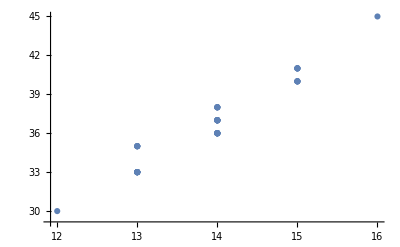

```mathematica
Table[
With[{g=EmbedGraphInPlantri8[k]},
{VertexCount[g],EdgeCount[g]}
],{k,allGraphs5AtomKeys}
]//Sort//ListPlot
```